{1→2,2→3,3→1,4→6,5→7,6→2,7→10,8→11,9→3,1→3,2→1,3→2,4→2,5→10,6→3,7→14,8→15,9→1,1→1,2→2,3→3,4→3,5→14,6→1,7→19,8→5,9→2,1→2,2→3,3→1,4→1,5→19,6→2,7→26,8→7,9→3,1→3,2→1,3→2,4→2,5→26,6→3,7→35,8→10,9→1,1→1,2→2,3→3,4→3,5→35,6→1,7→47,8→14,9→2,1→2,2→3,3→1,4→1,5→47,6→2,7→63,8→19,9→3,1→3,2→1,3→2,4→2,5→63,6→3,7→21,8→26,9→1,1→1,2→2,3→3,4→3,5→21,6→1,7→7,8→35,9→2}

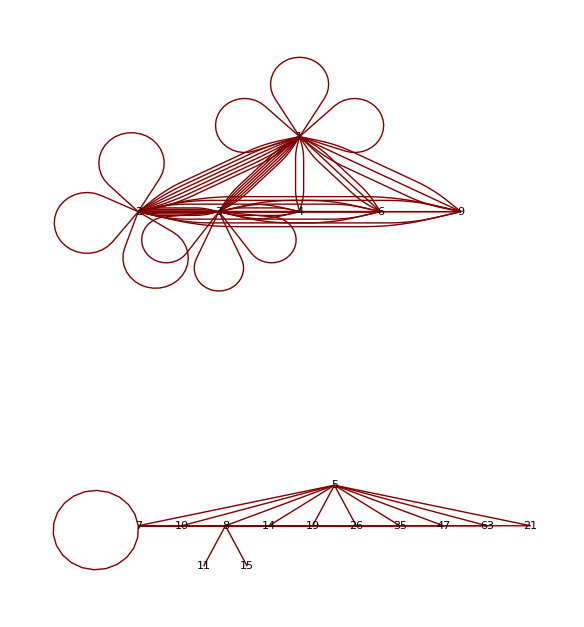

```mathematica
h[x_,y_]:=Piecewise[{{((y+1)x+y-Mod[x,y])/y, x/y∉Integers}, {x/y, x/y∈Integers}}]
j3[x_]:=h[x,3]
bb:=3
Monitor[Flatten[Table[x->Nest[j3,x,n],{n,1,bb^2},{x,1,bb^2}]],{n,x}]
TreePlot[%,VertexLabeling->True]
```

```mathematica
Nest[j3,1,3]
```

1

```mathematica
Nest[j3,7,8]
```

21

```mathematica
3*2+1
```

```mathematica
(B+1)x+B-c
```

```mathematica
6,9,10
```

{1→2,2→3,3→4,4→5,5→6,6→1,7→9,8→10,9→11,10→12,11→13,12→2,13→16,14→17,15→18,16→19,17→20,18→3,19→23,20→24,21→25,22→26,23→27,24→4,25→30,26→31,27→32,28→33,29→34,30→5,31→37,32→38,33→39,34→40,35→41,36→6,1→3,2→4,3→5,4→6,5→1,6→2,7→11,8→12,9→13,10→2,11→16,12→3,13→19,14→20,15→3,16→23,17→24,18→4,19→27,20→4,21→30,22→31,23→32,24→5,25→5,26→37,27→38,28→39,29→40,30→6,31→44,32→45,33→46,34→47,35→48,36→1,1→4,2→5,3→6,4→1,5→2,6→3,7→13,8→2,9→16,10→3,11→19,12→4,13→23,14→24,15→4,16→27,17→4,18→5,19→32,20→5,21→5,22→37,23→38,24→6,25→6,26→44,27→45,28→46,29→47,30→1,31→52,32→53,33→54,34→55,35→8,36→2,1→5,2→6,3→1,4→2,5→3,6→4,7→16,8→3,9→19,10→4,11→23,12→5,13→27,14→4,15→5,16→32,17→5,18→6,19→38,20→6,21→6,22→44,23→45,24→1,25→1,26→52,27→53,28→54,29→55,30→2,31→61,32→62,33→9,34→65,35→10,36→3,1→6,2→1,3→2,4→3,5→4,6→5,7→19,8→4,9→23,10→5,11→27,12→6,13→32,14→5,15→6,16→38,17→6,18→1,19→45,20→1,21→1,22→52,23→53,24→2,25→2,26→61,27→62,28→9,29→65,30→3,31→72,32→73,33→11,34→76,35→12,36→4,1→1,2→2,3→3,4→4,5→5,6→6,7→23,8→5,9→27,10→6,11→32,12→1,13→38,14→6,15→1,16→45,17→1,18→2,19→53,20→2,21→2,22→61,23→62,24→3,25→3,26→72,27→73,28→11,29→76,30→4,31→12,32→86,33→13,34→89,35→2,36→5,1→2,2→3,3→4,4→5,5→6,6→1,7→27,8→6,9→32,10→1,11→38,12→2,13→45,14→1,15→2,16→53,17→2,18→3,19→62,20→3,21→3,22→72,23→73,24→4,25→4,26→12,27→86,28→13,29→89,30→5,31→2,32→101,33→16,34→104,35→3,36→6,1→3,2→4,3→5,4→6,5→1,6→2,7→32,8→1,9→38,10→2,11→45,12→3,13→53,14→2,15→3,16→62,17→3,18→4,19→73,20→4,21→4,22→12,23→86,24→5,25→5,26→2,27→101,28→16,29→104,30→6,31→3,32→118,33→19,34→122,35→4,36→1,1→4,2→5,3→6,4→1,5→2,6→3,7→38,8→2,9→45,10→3,11→53,12→4,13→62,14→3,15→4,16→73,17→4,18→5,19→86,20→5,21→5,22→2,23→101,24→6,25→6,26→3,27→118,28→19,29→122,30→1,31→4,32→138,33→23,34→143,35→5,36→2,1→5,2→6,3→1,4→2,5→3,6→4,7→45,8→3,9→53,10→4,11→62,12→5,13→73,14→4,15→5,16→86,17→5,18→6,19→101,20→6,21→6,22→3,23→118,24→1,25→1,26→4,27→138,28→23,29→143,30→2,31→5,32→23,33→27,34→167,35→6,36→3,1→6,2→1,3→2,4→3,5→4,6→5,7→53,8→4,9→62,10→5,11→73,12→6,13→86,14→5,15→6,16→101,17→6,18→1,19→118,20→1,21→1,22→4,23→138,24→2,25→2,26→5,27→23,28→27,29→167,30→3,31→6,32→27,33→32,34→195,35→1,36→4,1→1,2→2,3→3,4→4,5→5,6→6,7→62,8→5,9→73,10→6,11→86,12→1,13→101,14→6,15→1,16→118,17→1,18→2,19→138,20→2,21→2,22→5,23→23,24→3,25→3,26→6,27→27,28→32,29→195,30→4,31→1,32→32,33→38,34→228,35→2,36→5,1→2,2→3,3→4,4→5,5→6,6→1,7→73,8→6,9→86,10→1,11→101,12→2,13→118,14→1,15→2,16→138,17→2,18→3,19→23,20→3,21→3,22→6,23→27,24→4,25→4,26→1,27→32,28→38,29→228,30→5,31→2,32→38,33→45,34→38,35→3,36→6,1→3,2→4,3→5,4→6,5→1,6→2,7→86,8→1,9→101,10→2,11→118,12→3,13→138,14→2,15→3,16→23,17→3,18→4,19→27,20→4,21→4,22→1,23→32,24→5,25→5,26→2,27→38,28→45,29→38,30→6,31→3,32→45,33→53,34→45,35→4,36→1,1→4,2→5,3→6,4→1,5→2,6→3,7→101,8→2,9→118,10→3,11→138,12→4,13→23,14→3,15→4,16→27,17→4,18→5,19→32,20→5,21→5,22→2,23→38,24→6,25→6,26→3,27→45,28→53,29→45,30→1,31→4,32→53,33→62,34→53,35→5,36→2,1→5,2→6,3→1,4→2,5→3,6→4,7→118,8→3,9→138,10→4,11→23,12→5,13→27,14→4,15→5,16→32,17→5,18→6,19→38,20→6,21→6,22→3,23→45,24→1,25→1,26→4,27→53,28→62,29→53,30→2,31→5,32→62,33→73,34→62,35→6,36→3,1→6,2→1,3→2,4→3,5→4,6→5,7→138,8→4,9→23,10→5,11→27,12→6,13→32,14→5,15→6,16→38,17→6,18→1,19→45,20→1,21→1,22→4,23→53,24→2,25→2,26→5,27→62,28→73,29→62,30→3,31→6,32→73,33→86,34→73,35→1,36→4,1→1,2→2,3→3,4→4,5→5,6→6,7→23,8→5,9→27,10→6,11→32,12→1,13→38,14→6,15→1,16→45,17→1,18→2,19→53,20→2,21→2,22→5,23→62,24→3,25→3,26→6,27→73,28→86,29→73,30→4,31→1,32→86,33→101,34→86,35→2,36→5,1→2,2→3,3→4,4→5,5→6,6→1,7→27,8→6,9→32,10→1,11→38,12→2,13→45,14→1,15→2,16→53,17→2,18→3,19→62,20→3,21→3,22→6,23→73,24→4,25→4,26→1,27→86,28→101,29→86,30→5,31→2,32→101,33→118,34→101,35→3,36→6,1→3,2→4,3→5,4→6,5→1,6→2,7→32,8→1,9→38,10→2,11→45,12→3,13→53,14→2,15→3,16→62,17→3,18→4,19→73,20→4,21→4,22→1,23→86,24→5,25→5,26→2,27→101,28→118,29→101,30→6,31→3,32→118,33→138,34→118,35→4,36→1,1→4,2→5,3→6,4→1,5→2,6→3,7→38,8→2,9→45,10→3,11→53,12→4,13→62,14→3,15→4,16→73,17→4,18→5,19→86,20→5,21→5,22→2,23→101,24→6,25→6,26→3,27→118,28→138,29→118,30→1,31→4,32→138,33→23,34→138,35→5,36→2,1→5,2→6,3→1,4→2,5→3,6→4,7→45,8→3,9→53,10→4,11→62,12→5,13→73,14→4,15→5,16→86,17→5,18→6,19→101,20→6,21→6,22→3,23→118,24→1,25→1,26→4,27→138,28→23,29→138,30→2,31→5,32→23,33→27,34→23,35→6,36→3,1→6,2→1,3→2,4→3,5→4,6→5,7→53,8→4,9→62,10→5,11→73,12→6,13→86,14→5,15→6,16→101,17→6,18→1,19→118,20→1,21→1,22→4,23→138,24→2,25→2,26→5,27→23,28→27,29→23,30→3,31→6,32→27,33→32,34→27,35→1,36→4,1→1,2→2,3→3,4→4,5→5,6→6,7→62,8→5,9→73,10→6,11→86,12→1,13→101,14→6,15→1,16→118,17→1,18→2,19→138,20→2,21→2,22→5,23→23,24→3,25→3,26→6,27→27,28→32,29→27,30→4,31→1,32→32,33→38,34→32,35→2,36→5,1→2,2→3,3→4,4→5,5→6,6→1,7→73,8→6,9→86,10→1,11→101,12→2,13→118,14→1,15→2,16→138,17→2,18→3,19→23,20→3,21→3,22→6,23→27,24→4,25→4,26→1,27→32,28→38,29→32,30→5,31→2,32→38,33→45,34→38,35→3,36→6,1→3,2→4,3→5,4→6,5→1,6→2,7→86,8→1,9→101,10→2,11→118,12→3,13→138,14→2,15→3,16→23,17→3,18→4,19→27,20→4,21→4,22→1,23→32,24→5,25→5,26→2,27→38,28→45,29→38,30→6,31→3,32→45,33→53,34→45,35→4,36→1,1→4,2→5,3→6,4→1,5→2,6→3,7→101,8→2,9→118,10→3,11→138,12→4,13→23,14→3,15→4,16→27,17→4,18→5,19→32,20→5,21→5,22→2,23→38,24→6,25→6,26→3,27→45,28→53,29→45,30→1,31→4,32→53,33→62,34→53,35→5,36→2,1→5,2→6,3→1,4→2,5→3,6→4,7→118,8→3,9→138,10→4,11→23,12→5,13→27,14→4,15→5,16→32,17→5,18→6,19→38,20→6,21→6,22→3,23→45,24→1,25→1,26→4,27→53,28→62,29→53,30→2,31→5,32→62,33→73,34→62,35→6,36→3,1→6,2→1,3→2,4→3,5→4,6→5,7→138,8→4,9→23,10→5,11→27,12→6,13→32,14→5,15→6,16→38,17→6,18→1,19→45,20→1,21→1,22→4,23→53,24→2,25→2,26→5,27→62,28→73,29→62,30→3,31→6,32→73,33→86,34→73,35→1,36→4,1→1,2→2,3→3,4→4,5→5,6→6,7→23,8→5,9→27,10→6,11→32,12→1,13→38,14→6,15→1,16→45,17→1,18→2,19→53,20→2,21→2,22→5,23→62,24→3,25→3,26→6,27→73,28→86,29→73,30→4,31→1,32→86,33→101,34→86,35→2,36→5,1→2,2→3,3→4,4→5,5→6,6→1,7→27,8→6,9→32,10→1,11→38,12→2,13→45,14→1,15→2,16→53,17→2,18→3,19→62,20→3,21→3,22→6,23→73,24→4,25→4,26→1,27→86,28→101,29→86,30→5,31→2,32→101,33→118,34→101,35→3,36→6,1→3,2→4,3→5,4→6,5→1,6→2,7→32,8→1,9→38,10→2,11→45,12→3,13→53,14→2,15→3,16→62,17→3,18→4,19→73,20→4,21→4,22→1,23→86,24→5,25→5,26→2,27→101,28→118,29→101,30→6,31→3,32→118,33→138,34→118,35→4,36→1,1→4,2→5,3→6,4→1,5→2,6→3,7→38,8→2,9→45,10→3,11→53,12→4,13→62,14→3,15→4,16→73,17→4,18→5,19→86,20→5,21→5,22→2,23→101,24→6,25→6,26→3,27→118,28→138,29→118,30→1,31→4,32→138,33→23,34→138,35→5,36→2,1→5,2→6,3→1,4→2,5→3,6→4,7→45,8→3,9→53,10→4,11→62,12→5,13→73,14→4,15→5,16→86,17→5,18→6,19→101,20→6,21→6,22→3,23→118,24→1,25→1,26→4,27→138,28→23,29→138,30→2,31→5,32→23,33→27,34→23,35→6,36→3,1→6,2→1,3→2,4→3,5→4,6→5,7→53,8→4,9→62,10→5,11→73,12→6,13→86,14→5,15→6,16→101,17→6,18→1,19→118,20→1,21→1,22→4,23→138,24→2,25→2,26→5,27→23,28→27,29→23,30→3,31→6,32→27,33→32,34→27,35→1,36→4,1→1,2→2,3→3,4→4,5→5,6→6,7→62,8→5,9→73,10→6,11→86,12→1,13→101,14→6,15→1,16→118,17→1,18→2,19→138,20→2,21→2,22→5,23→23,24→3,25→3,26→6,27→27,28→32,29→27,30→4,31→1,32→32,33→38,34→32,35→2,36→5}

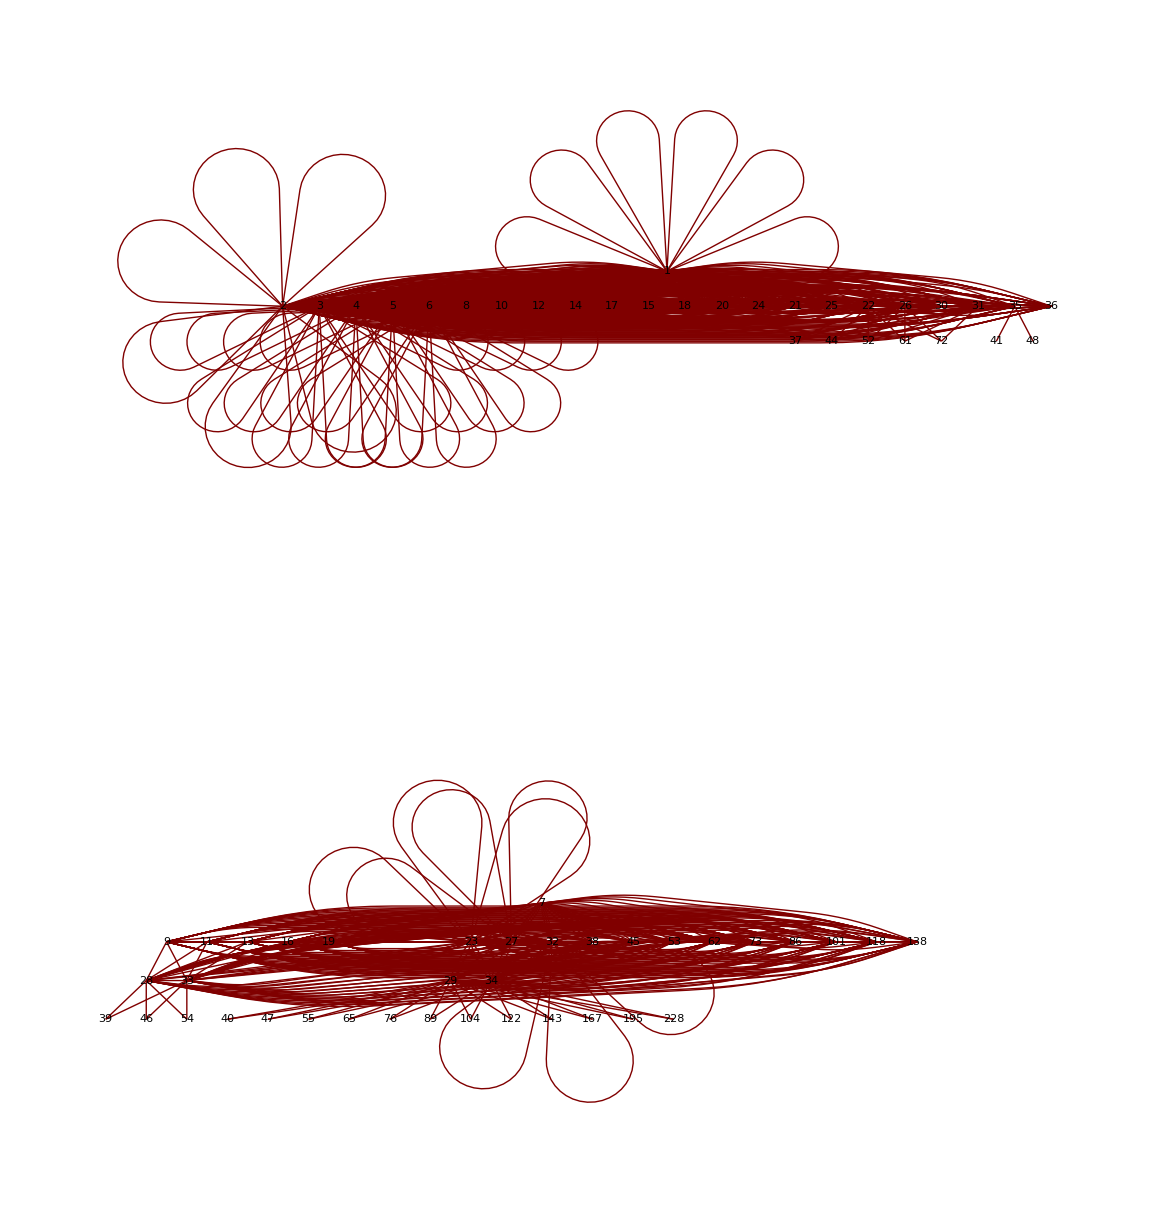

```mathematica
j6[x_]:=h[x,6]
bb:=6
Monitor[Flatten[Table[x->Nest[j6,x,n],{n,1,bb^2},{x,1,bb^2}]],{n,x}]
TreePlot[%,VertexLabeling->True]
```

```mathematica
Nest[j6,1,6]
```

1

```mathematica
Nest[j6,23,11]
```

138

```mathematica
138/23
```

6

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→1,10→12,11→13,12→14,13→15,14→16,15→17,16→18,17→19,18→2,19→22,20→23,21→24,22→25,23→26,24→27,25→28,26→29,27→3,28→32,29→33,30→34,31→35,32→36,33→37,34→38,35→39,36→4,37→42,38→43,39→44,40→45,41→46,42→47,43→48,44→49,45→5,46→52,47→53,48→54,49→55,50→56,51→57,52→58,53→59,54→6,55→62,56→63,57→64,58→65,59→66,60→67,61→68,62→69,63→7,64→72,65→73,66→74,67→75,68→76,69→77,70→78,71→79,72→8,73→82,74→83,«6413»,8→8,9→9,10→6,11→3,12→7,13→4,14→8,15→5,16→9,17→6,18→1,19→7,20→9,21→9,22→8,23→1,24→1,25→9,26→2,27→2,28→1,29→3,30→9,31→228,32→2,33→4,34→1,35→254,36→3,37→5,38→2,39→283,40→3,41→3,42→6,43→3,44→315,45→4,46→4,47→7,48→4,49→35,50→4,51→4,52→5,53→8,54→5,55→39,56→5,57→5,58→6,59→9,60→6,61→3,62→44,63→6,64→6,65→7,66→1,67→7,68→4,69→49,70→2,71→6,72→7,73→8,74→2,75→8,76→5,77→55,78→3,79→7,80→9,81→8}

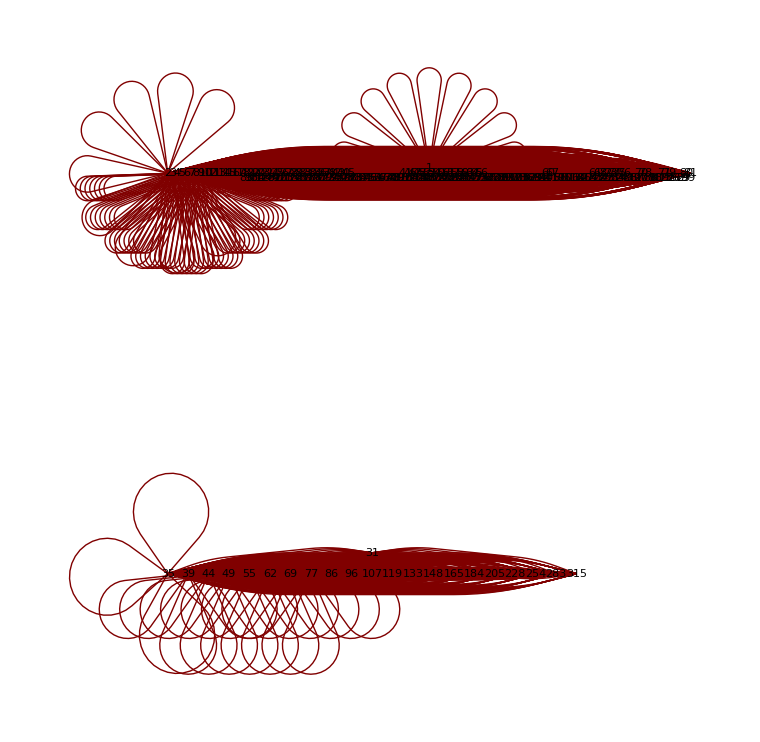

```mathematica
j9[x_]:=h[x,9]
bb:=9
Monitor[Flatten[Table[x->Nest[j9,x,n],{n,1,bb^2},{x,1,bb^2}]],{n,x}]
TreePlot[%,VertexLabeling->True]
```

```mathematica
Nest[j9,1,9]
```

1

```mathematica
Nest[j9,35,20]
```

```mathematica
315/9
```

35

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→1,11→13,12→14,13→15,14→16,15→17,16→18,17→19,18→20,19→21,20→2,21→24,22→25,23→26,24→27,25→28,26→29,27→30,28→31,29→32,30→3,31→35,32→36,33→37,34→38,35→39,36→40,37→41,38→42,39→43,40→4,41→46,42→47,43→48,44→49,45→50,46→51,47→52,48→53,49→54,50→5,51→57,52→58,53→59,54→60,55→61,56→62,57→63,58→64,59→65,60→6,61→68,62→69,63→70,64→71,65→72,66→73,67→74,68→75,69→76,70→7,71→79,72→80,«9856»,29→10,30→2,31→8,32→1,33→9,34→42,35→9,36→2,37→10,38→47,39→10,40→3,41→1,42→52,43→1,44→2,45→3,46→2,47→58,48→2,49→3,50→4,51→3,52→64,53→3,54→4,55→742,56→10,57→4,58→71,59→4,60→5,61→817,62→1,63→5,64→79,65→5,66→5,67→6,68→899,69→2,70→6,71→87,72→6,73→6,74→7,75→989,76→3,77→1,78→8,79→96,80→7,81→7,82→8,83→1088,84→4,85→2,86→9,87→106,88→10,89→2,90→8,91→9,92→1197,93→5,94→3,95→10,96→117,97→1,98→3,99→4,100→9}

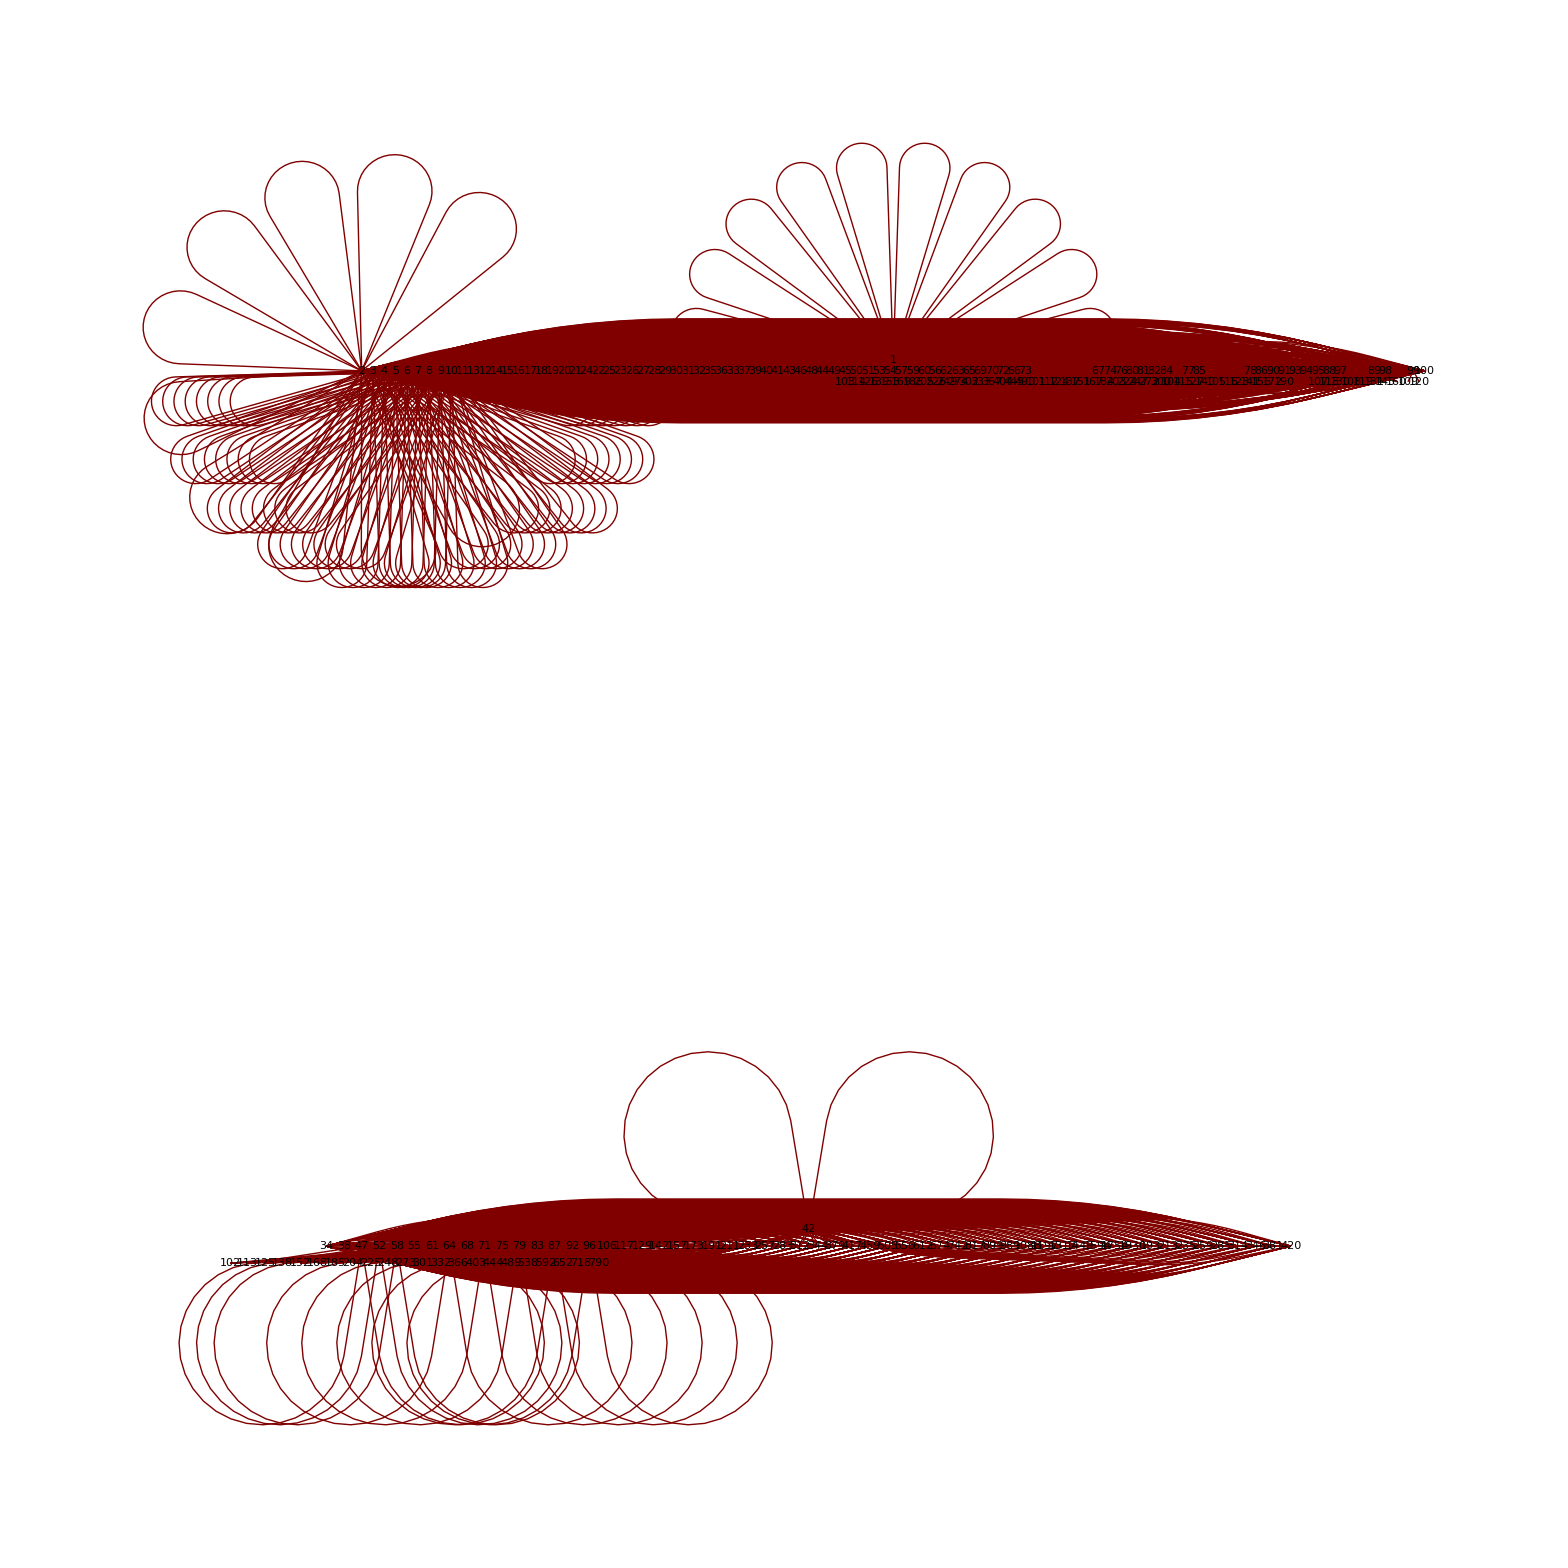

```mathematica
j10[x_]:=h[x,10]
bb:=10
Monitor[Flatten[Table[x->Nest[j10,x,n],{n,1,bb^2},{x,1,bb^2}]],{n,x}]
TreePlot[%,VertexLabeling->True]
```

```mathematica
Nest[j10,1,10]
```

1

```mathematica
Nest[j10,42,97]
```

420

```mathematica
h[x_,y_]:=Piecewise[{{((y+1)x+y-Mod[x,y])/y, x/y∉Integers}, {x/y, x/y∈Integers}}]
j20[x_]:=h[x,20]
bb:=20
Monitor[Flatten[Table[x->Nest[j20,x,n],{n,1,bb^2},{x,1,bb^2}]],{n,x}]
TreePlot[%,VertexLabeling->True]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→1,21→23,22→24,23→25,24→26,25→27,26→28,«159948»,375→7,376→17,377→6,378→12,379→16,380→18,381→135,382→6,383→18,384→18,385→7,386→7,387→8,388→10,389→18,390→12,391→10,392→2102,393→142,394→8,395→18,396→7,397→13,398→17,399→9,400→19}

-Graphics-

```mathematica
FactorInteger[{1,71,141}]
```

{{{1,1}},{{71,1}},{{3,1},{47,1}}}

```mathematica
Nest[j20,1,20]
```

1

```mathematica
Nest[j20,71,59]
```

1420

```mathematica
Nest[j20,141,60]
```

2820

```mathematica
Mod[71,20]
```

11

```mathematica
FactorInteger[70]
```

{{2,1},{5,1},{7,1}}

```mathematica
20*3+11
```

71

```mathematica
FactorInteger[126]
```

{{2,1},{3,2},{7,1}}

```mathematica
3,8
6,11
9,20
10,97
```

```mathematica
2x -> +3
3x -> +12
```

```mathematica
RSolve[{f[n+1]==Subscript[a, n]*f[n]+Subscript[b, n],f[0]==x},f[n],n]
```

{{f[n]→x ∏_(K[1]=1)^(-1+n) a_K[1]+(∏_(K[1]=1)^(-1+n) a_K[1]) ∑_(K[2]=0)^(-1+n) b_K[2]/(∏_(K[1]=1)^K[2] a_K[1])}}

```mathematica
j3[4]
```

6

```mathematica
j3[6]
```

2

```mathematica
j3[5]
```

7

```mathematica
j3[7]
```

10

```mathematica
j3[10]
```

14

```mathematica
j3[14]
```

19

```mathematica
j3[19]
```

26

```mathematica
j3[26]
```

35

```mathematica
j3[35]
```

47

```mathematica
j3[47]
```

63

```mathematica
j3[63]
```

21

```mathematica
j3[21]
```

7